```mathematica
RbfK[l_,n_]:=Table[Exp[-(i-j)^2/(2 l)],{i,-1,1,2/(n-1)},{j,-1,1,2/(n-1)}]

RbfK[.2,5]//MatrixForm
```

(1. | 0.535261 | 0.082085 | 0.00360656 | 0.0000453999
0.535261 | 1. | 0.535261 | 0.082085 | 0.00360656
0.082085 | 0.535261 | 1. | 0.535261 | 0.082085
0.00360656 | 0.082085 | 0.535261 | 1. | 0.535261
0.0000453999 | 0.00360656 | 0.082085 | 0.535261 | 1.)

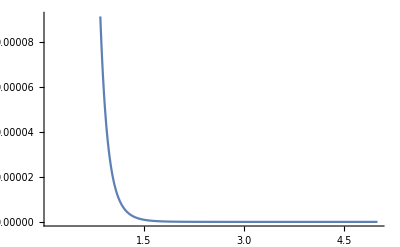

```mathematica
Plot[Det[RbfK[l,5]],{l,.1,5}]
```

```mathematica
Det[RbfK[.01,5]]
```

1.

```mathematica
N[Det[RbfK[50,5]+.1 IdentityMatrix[5]]]
```

0.000754664